```mathematica
(* IMPORT MODULES *)
ClearAll[m1,m2,m3]
loadDumpSaves=True;
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["modules/oscillator_bracket.nb"];
NotebookEvaluate["modules/mews_and_alphas.nb"];
NotebookEvaluate["modules/operators.nb"];
NotebookEvaluate["modules/hamiltonian.nb"];
NotebookEvaluate["modules/parameters.nb"];
NotebookEvaluate["modules/golden_search.nb"];
If[loadDumpSaves,NotebookEvaluate["modules/load_dump_saves.nb"]];
SetDirectory[NotebookDirectory[]];
```

```mathematica
datas={};
For[i=0,i≤6,i++,
(*NotebookEvaluate["modules/oscillator_bracket.nb"];*)
times=AbsoluteTiming[tMatrix[1/2,1,0,1/2,i*2,1.0,2.0,3.0,1]];
data=times[[1]];
AppendTo[datas,{Length[times[[2]]],data}]
]
```

```mathematica
datas
```

{{2,0.0008},{8,0.003778},{20,0.017545},{40,0.039652},{70,0.09445},{112,0.22946},{168,0.496402}}

```mathematica
Export["lines/ch1b_talmi_times_second_run.mx",datas]
```

lines/ch1b_talmi_times_second_run.mx

```mathematica
data1=Import["lines/ch1b_talmi_times_first_run.mx"]
data2=Import["lines/ch1b_talmi_times_second_run.mx"]
```

{{2,0.010584},{8,0.017202},{20,0.081836},{40,0.560317},{70,4.9664},{112,33.2987},{168,203.593}}

{{2,0.0008},{8,0.003778},{20,0.017545},{40,0.039652},{70,0.09445},{112,0.22946},{168,0.496402}}

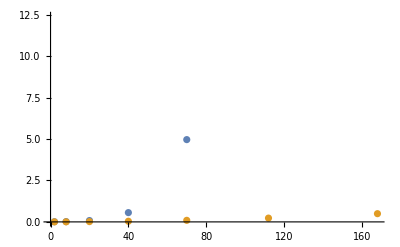

```mathematica
ListPlot[{data1,data2}]
```

```mathematica
Fit[datas,{1,x,x^2},x]
```

0.00599015+0.000185485 x+0.0000171106 x^2

```mathematica
par2[x_]:=0.005990148112097477+0.00018548466307120737 x+0.00001711063777286347 x^2
fit=Table[{x,par2[x]},{x,0,168,0.01}];
```

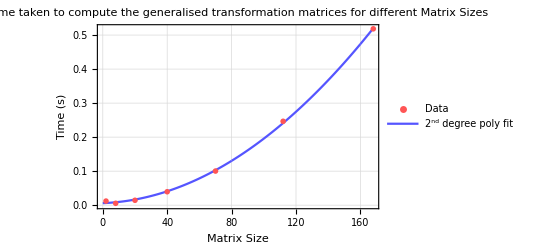

```mathematica
plot=ListPlot[{datas,fit},Joined->{False,True},PlotTheme->"Detailed",PlotRange->All,
PlotLabel->"Time taken to compute the generalised\ntransformation matrices for different Matrix Sizes",
FrameLabel->{"Matrix Size","Time (s)"},
PlotStyle->{Lighter[Red],Lighter[Blue]},
PlotMarkers->{{Automatic,0.04},None},
PlotLegends->Placed[{"Data","2^nd degree poly fit"},{Left,Top}]]
```

```mathematica
Export["plots/ch1b_time_complexity_talmi.pdf",plot,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

plots/ch1b_time_complexity_talmi.pdf

```mathematica
datas={};
For[i=1,i≤30,i++,
NotebookEvaluate["modules/operators.nb"];
times=Table[AbsoluteTiming[rel[n,n,0,2]],{n,0,100}];
data=times[[All,1]];
AppendTo[datas,data]
]
```

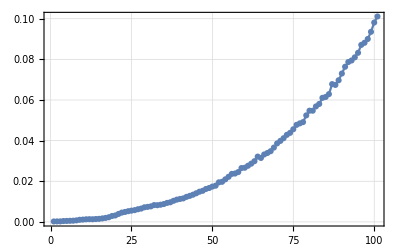

```mathematica
ListPlot[Mean[datas], Joined->True,PlotMarkers->Automatic,PlotTheme->"Detailed"]
```

```mathematica
parabola=Fit[Mean[datas],{1,x,x^2,x^3},x]
```

-0.000801962+0.000214224 x-1.35606×10^-6 x^2+8.96074×10^-8 x^3

```mathematica
par[x_]:=-0.0008019615412969741+0.00021422383760588573 x-1.3560585552408076*^-6 x^2+8.960739427086806*^-8 x^3
fit=Table[{x,par[x]},{x,0,101,0.01}];
```

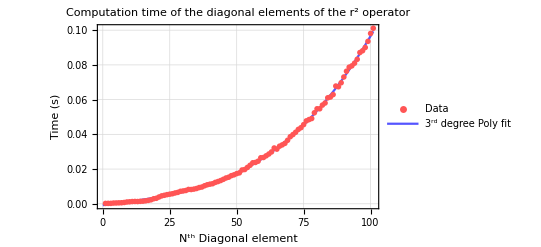

```mathematica
plot=ListPlot[{Mean[datas],fit},Joined->{False,True},PlotTheme->"Detailed",
PlotLabel->"Computation time of the diagonal elements of the r^2 operator",
FrameLabel->{"N^th Diagonal element","Time (s)"},
PlotStyle->{Lighter[Red],Lighter[Blue]},
PlotMarkers->{{Automatic,0.022},None},
PlotLegends->Placed[{"Data","3^rd degree Poly fit"},{Left,Top}]]
```

```mathematica
Export["plots/ch1b_time_complexity_ry.pdf",plot,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

plots/ch1b_time_complexity_ry.pdf

```mathematica
datas={};
For[gamma=0,gamma≤6,gamma++,
NotebookEvaluate["modules/operators.nb"];
sM=stateMatrix[1/2,1,0,1/2,gamma*2];
result=AbsoluteTiming[polynomialOperatorRho[sM,2]];
data=result[[1]];
AppendTo[datas,{Length[sM],data}]
]
```

```mathematica
datas
```

{{2,0.000209},{8,0.000978},{20,0.006967},{40,0.013791},{70,0.039807},{112,0.08277},{168,0.180186},{240,0.357476},{330,0.655957}}

```mathematica
Fit[datas,{1,x,x^2},x]
```

0.000626729+0.0000226854 x+6.54123×10^-6 x^2

```mathematica
par2[x_]:=0.0006267287339406154+0.000022685377785389317 x+6.541227589084801*^-6 x^2
fit=Table[{x,par2[x]},{x,0,168,0.01}];
```

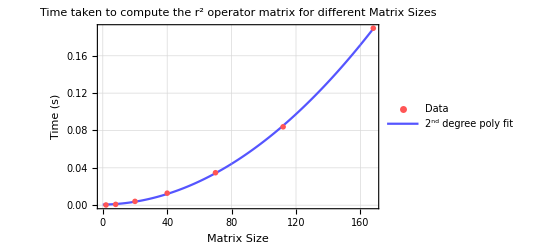

```mathematica
plot=ListPlot[{datas,fit},Joined->{False,True},PlotTheme->"Detailed",
PlotLabel->"Time taken to compute the r^2 operator matrix\nfor different Matrix Sizes",
FrameLabel->{"Matrix Size","Time (s)"},
PlotStyle->{Lighter[Red],Lighter[Blue]},
PlotMarkers->{{Automatic,0.04},None},
PlotLegends->Placed[{"Data","2^nd degree poly fit"},{Left,Top}]]
```

```mathematica
Export["plots/ch1b_time_complexity_ry_matrix.pdf",plot,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

plots/ch1b_time_complexity_ry_matrix.pdf

```mathematica
datas={};
For[gamma=0,gamma≤6,gamma++,
NotebookEvaluate["modules/operators.nb"];
sM=stateMatrix[1/2,1,0,1/2,gamma*2];
result=AbsoluteTiming[GaussOperator[sM,1.0,1.0]];
data=result[[1]];
AppendTo[datas,{Length[sM],data}]
]
```

```mathematica
Fit[datas,{1,x,x^2},x]
```

0.00438418-0.00040617 x+0.0000275845 x^2

```mathematica
par2[x_]:=0.00438417700411495-0.0004061701482812028 x+0.00002758446923180199 x^2
fit=Table[{x,par2[x]},{x,0,168,0.01}];
```

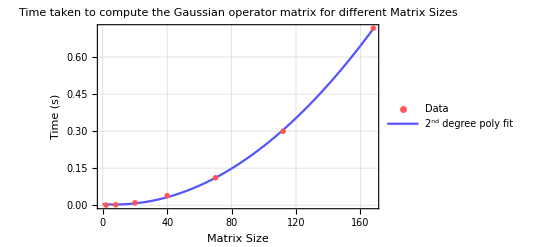

```mathematica
plot=ListPlot[{datas,fit},Joined->{False,True},PlotTheme->"Detailed",
PlotLabel->"Time taken to compute the Gaussian operator \n matrix for different Matrix Sizes",
FrameLabel->{"Matrix Size","Time (s)"},
PlotStyle->{Lighter[Red],Lighter[Blue]},
PlotMarkers->{{Automatic,0.04},None},
PlotLegends->Placed[{"Data","2^nd degree poly fit"},{Left,Top}]]
```

```mathematica
Export["plots/ch1b_time_complexity_gaussian_matrix.pdf",plot,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

plots/ch1b_time_complexity_gaussian_matrix.pdf

```mathematica
?ExponentialOperator
```

```mathematica
datas={};
For[gamma=0,gamma≤6,gamma++,
NotebookEvaluate["modules/operators.nb"];
sM=stateMatrix[1/2,1,0,1/2,gamma*2];
result=AbsoluteTiming[ExponentialOperator[sM,0,0.5,0.5]];
data=result[[1]];
AppendTo[datas,{Length[sM],data}]
]
```

```mathematica
Fit[datas,{1,x,x^2,x^3},x]
```

0.0306767-0.0054679 x+0.000360742 x^2+2.39772×10^-7 x^3

```mathematica
par2[x_]:=0.030676737324486853-0.0054679006190700916 x+0.00036074189359417373 x^2+2.397721554943804*^-7 x^3
fit=Table[{x,par2[x]},{x,0,168,0.01}];
```

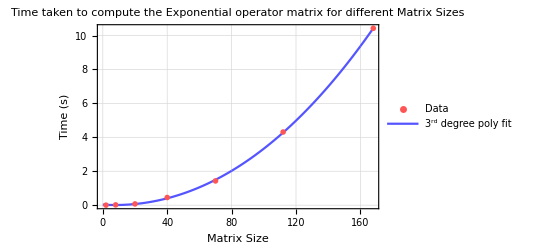

```mathematica
plot=ListPlot[{datas,fit},Joined->{False,True},PlotTheme->"Detailed",
PlotLabel->"Time taken to compute the Exponential operator \n matrix for different Matrix Sizes",
FrameLabel->{"Matrix Size","Time (s)"},
PlotStyle->{Lighter[Red],Lighter[Blue]},
PlotMarkers->{{Automatic,0.04},None},
PlotLegends->Placed[{"Data","3^rd degree poly fit"},{Left,Top}]]
```

```mathematica
Export["plots/ch1b_time_complexity_exp_matrix.pdf",plot,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

plots/ch1b_time_complexity_exp_matrix.pdf

```mathematica
HamiltonianMin[J_,P_,FlavourSym_,γMax_,Λ_,S_,m1_,m2_,m3_,excited_,temperature_,wLeft_,wRight_,tolerance_,whichHamiltonian_:1,optimise_:True,omega_:1]:=Module[{},
ClearAll[case,proj,vCoulomb,vLinear,qhoSpect,kineticRho,kineticLam,wMin,hamiltonian,ham,sM,t1,t2,states,sM];
(* all different masses = 0, two equal masses = 1, all equal masses = 2 *)
case=If[m1==m2,1,0];
case=If[m1==m2==m3,2,case];
states=allStates[J,P,Λ,S,γMax];
sM=stateMatrix[J,P,Λ,S,γMax];

(* Calculate generalised transformation matrices *)
{t1time,t1}=AbsoluteTiming[tMatrix[J,P,Λ,S,γMax,m1,m2,m3,1]];
Print["Time taken to compute t1: ", ToString[t1time]];
{t2time,t2}=AbsoluteTiming[tMatrix[J,P,Λ,S,γMax,m1,m2,m3,2]];
Print["Time taken to compute t2: ", ToString[t2time]];

(* Obtain projector matrix *)
proj=projector[states,FlavourSym,case];
vCoulomb=polynomialOperatorRho[sM,-1];(* 1/ρ matrix dimensionless *)
vLinear=polynomialOperatorRho[sM,1];(* ρ matrix dimensionless *)
(* Required matrices for hamiltonian *)
qhoSpect=qhoSpectrum[sM];
kineticRho=polynomialOperatorRho[sM,2];
kineticLam=polynomialOperatorLambda[sM,2];

(* Choose which Hamiltonian to use (simple temp dependence = 1, Debye screened potential = 2) *)
If[whichHamiltonian==1,
(* Hamiltonian matrix *)
ham[ω_]:=Hb[ω,temperature,m1,m2,m3,proj],
ham[ω_]:=Hb2[ω,temperature,m1,m2,m3]
];

If[optimise,
(* Find minimum and errors*)
{minTime,{a,b,data}}=AbsoluteTiming[goldenSearch[ham,excited+1,wLeft,wRight,tolerance]];
(*Print["Time taken to find minimum: ", ToString[minTime],"s"];*)
wMin=(a+b)/2;
hamiltonian=ham[wMin],
hamiltonian=ham[omega]
];
(*eigvalMin=Eigenvalues[hamiltonian][[-excited-1]];
Print["{ω_min, E_min}: ",{Around[wMin,a-wMin],eigvalMin}];
Print["Number of basis functions (matrix size): ", Length[hamiltonian]]*)

(* Dump Saves, must only be saved if loadDumpSaves is True *)
If[loadDumpSaves,
DumpSave["modules/dumpSave/summationVariables.mx",summationVariables];
DumpSave["modules/dumpSave/talmi.mx",talmi];
DumpSave["modules/dumpSave/nineJ.mx",nineJ];
DumpSave["modules/dumpSave/rel.mx",rel];
DumpSave["modules/dumpSave/Rcoeff.mx",Rcoeff];
DumpSave["modules/dumpSave/Lcoeff.mx",Lcoeff];
];
hamiltonian
]
```

```mathematica
(* Eigenvectors of the Subscript[Λ, c] baryon excited states *)
(**** !!!TUNABLE PARAMETERS!!! ****)
m1=uq;(* mass of quark 1 *)
m2=uq;(* mass of quark 2 *)
m3=cq;(* mass of quark 3 *)
J=1/2;(* Total angular momentum J = Λ + S *)
Λ=0;(* Total orbital angular momentum Λ = Subscript[l, ρ] + Subscript[l, λ] *)
S=1/2;(* Total spin *)
P=+1;(* Parity P=(-1)^(Subscript[l, ρ]+Subscript[l, λ]) *)
FlavourSym=0;(* Flavour symmetry 1 = symmetric, 0 = antisymmetric *)
γMax=0;(* Maximum energy of considered basis states (2n+l+2N+L), use this to control Subscript[N, Q] *)
excited=0;(* Choose excited state, 0 for ground state *)
temperature=0; (* Temperature *)
wLeft=0.0001; (* golden search range left *)
wRight=0.9; (* golden search range right *)
tolerance=0.0005;(* golden search tolerance *)
model=1;(* Which model to use *)
optim=False; (* To optimise ω, True or False *)
w=1.0; (* If optim not True, what value of omega to use? *)
(**** !!! END OF TUNABLE PARAMETERS!!! ****)

timeData={};
For[run=0,run≤6,run++,
ham=AbsoluteTiming[HamiltonianMin[J,P,FlavourSym,run*2,Λ,S,m1,m2,m3,excited,temperature,wLeft,wRight,tolerance,whichHamiltonian=model,optimise=optim,omega=w]];
Print[ham[[1]]];
AppendTo[timeData,{run*2,ham[[1]]}]
]
```

Time taken to compute t1: 0.01164

Time taken to compute t2: 0.003832

0.104331

Time taken to compute t1: 0.006073

Time taken to compute t2: 0.002653

0.096604

Time taken to compute t1: 0.013199

Time taken to compute t2: 0.01186

0.136423

Time taken to compute t1: 0.040342

Time taken to compute t2: 0.036554

0.267822

Time taken to compute t1: 0.101379

Time taken to compute t2: 0.098572

0.652222

Time taken to compute t1: 0.239413

Time taken to compute t2: 0.229994

1.54048

Time taken to compute t1: 0.512201

Time taken to compute t2: 0.499575

3.4255

```mathematica
timeData
```

{{0,0.104331},{2,0.096604},{4,0.136423},{6,0.267822},{8,0.652222},{10,1.54048},{12,3.4255}}

```mathematica
Fit[timeData,{1,x,x^2,x^3,x^4},x]
```

0.10562-0.0367876 x+0.0213846 x^2-0.00394006 x^3+0.000361144 x^4

```mathematica
par2[x_]:=0.10561957359307404-0.03678764754689792 x+0.021384592803030487 x^2-0.003940056186868708 x^3+0.0003611444128787887 x^4
fit=Table[{x,par2[x]},{x,0,12,0.01}];
```

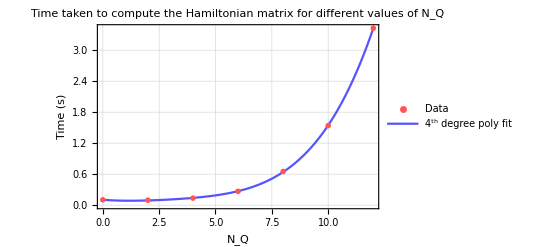

```mathematica
plot=ListPlot[{timeData,fit},Joined->{False,True},PlotTheme->"Detailed",PlotRange->All,
PlotLabel->"Time taken to compute the Hamiltonian matrix\nfor different values of N_Q",
FrameLabel->{"N_Q","Time (s)"},
PlotStyle->{Lighter[Red],Lighter[Blue]},
PlotMarkers->{{Automatic,0.04},None},
PlotLegends->Placed[{"Data","4^th degree poly fit"},{Left,Top}]]
```

```mathematica
Export["plots/ch1b_time_complexity_hamil.pdf",plot,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

plots/ch1b_time_complexity_hamil.pdf